```mathematica
SetDirectory[NotebookDirectory[]]
Get["AES-implementation.wl"]
```

/Users/marco/marco.live/DIDATTICA/CORSI/2023-2024/MDA/cryptoCS/code/MDA-2024

(152 | 89 | 111 | 233
165 | 38 | 192 | 189
21 | 87 | 0 | 117
220 | 240 | 122 | 105)

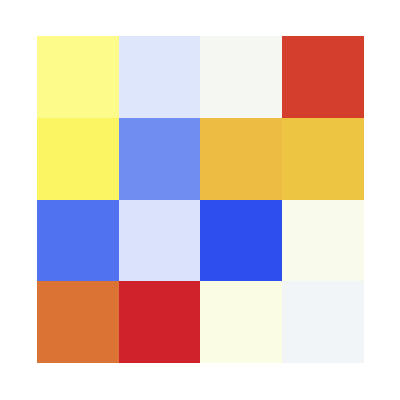

```mathematica
state0=Table[RandomInteger[255],{4},{4}];
state0//MatrixForm
ArrayPlot[state0,ColorFunction->"TemperatureMap"]
```

(152 | 89 | 111 | 233
165 | 38 | 192 | 189
21 | 87 | 0 | 117
220 | 240 | 122 | 105)

True

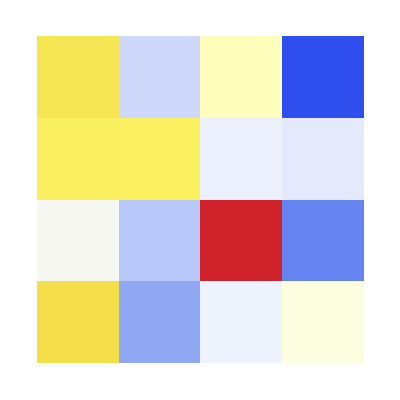

```mathematica
state0//MatrixForm
state1=SubBytes[state0];
state0==InverseSubBytes[state1]

ArrayPlot[state1,ColorFunction->"TemperatureMap"]
```

(148 | 76 | 122 | 17
143 | 91 | 87 | 144
198 | 41 | 101 | 69
111 | 152 | 56 | 93)

True

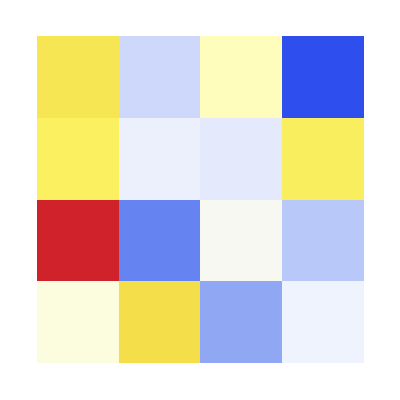

```mathematica
state2=ShiftRows[state1];
state2//MatrixForm
state1==InverseShiftRows[state2]
ArrayPlot[state2,ColorFunction->"TemperatureMap"]
```

(16 | 196 | 80 | 145
175 | 25 | 67 | 184
61 | 246 | 175 | 236
48 | 141 | 204 | 92)

True

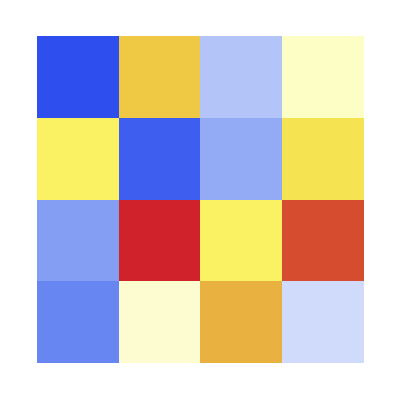

```mathematica
state3=MixColumns[state2];
state3//MatrixForm
state2==InverseMixColumns[state3]
ArrayPlot[state3,ColorFunction->"TemperatureMap"]
```

```mathematica
mtab=Table[FieldTimes[a,b],{a,0,255},{b,0,255}];
mtab//MatrixForm
ArrayPlot[mtab,ColorFunction->"TemperatureMap"]
```

```mathematica
key="DEADBEEF0001020304AABBCCDDC0DEF0";
```

```mathematica
image=Import["https://www.lacomunicazione.it/fotobig/1140_1.jpg"];
```

```mathematica
data=ImageData[image,"Byte"];
Dimensions[data]
```

{438,436,3}

```mathematica
X=Flatten[data];
message=Partition[Partition[X,4],4];
```

```mathematica
key
ctx=ParallelMap[AESEncryption[key,#]&,message];
```

DEADBEEF0001020304AABBCCDDC0DEF0

```mathematica
message[[1]]
ct=AESEncryption[key,message[[1]]]
AESDecryption[key,ct]
```

{{231,231,231,234},{234,234,227,227},{227,238,238,238},{238,238,238,238}}

{{157,220,183,140},{236,42,28,104},{117,243,50,134},{229,206,160,55}}

{{231,231,231,234},{234,234,227,227},{227,238,238,238},{238,238,238,238}}

```mathematica
X2=Partition[Partition[Flatten[ctx],3],438]
G1=Image[X2,"Byte"]
```

-Graphics-

```mathematica
ImageCompose[image, {G1,0.7}]
```

-Graphics-

```mathematica
AESKeySchedule[key,10]
```

{{{222,0,4,221},{173,1,170,192},{190,2,187,222},{239,3,204,240}},{{132,132,128,93},{140,141,39,231},{134,132,63,225},{3,0,204,60}},{{63,187,59,102},{243,126,89,190},{200,76,115,146},{55,55,251,199}},{{33,154,161,199},{247,137,208,110},{84,24,107,249},{244,195,56,255}},{{32,186,27,220},{158,23,199,169},{197,221,182,79},{104,171,147,108}},{{253,71,92,128},{38,49,246,95},{48,237,91,20},{240,91,200,164}},{{209,150,202,74},{121,72,190,225},{84,185,226,246},{220,135,79,235}},{{238,120,178,248},{173,229,91,186},{58,131,97,151},{65,198,137,98}},{{209,169,27,227},{213,48,107,209},{96,227,130,21},{165,99,234,136}},{{194,107,112,147},{176,128,235,58},{220,63,189,168},{68,39,205,69}},{{58,81,33,178},{108,236,7,61},{202,245,72,224},{121,94,147,214}}}

```mathematica
?AESEncryption
```

```mathematica
?AESRound
```

```mathematica
rk=AESKeySchedule[key,10][[1]]
```

{{222,0,4,221},{173,1,170,192},{190,2,187,222},{239,3,204,240}}

```mathematica
AddKey[MixColumns@ShiftRows@SubBytes[message[[1]]],rk]
```

AddKey[{{234,86,67,206},{81,132,42,167},{194,42,23,52},{136,103,114,157}},{{222,0,4,221},{173,1,170,192},{190,2,187,222},{239,3,204,240}}]

```mathematica
ptx=ParallelMap[AESDecryption[key,#]&,ctx];
```